```mathematica
ClearAll["Global`*"]
```

```mathematica
PathMD="/home/eixeres/Downloads/densmaps2_fine/";
input = Import[PathMD<>"Contact_Angles.dat"];
Length[input]
```

491

```mathematica
t51000=input[[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40},2]]
t52000=input[[{42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81},2]];
t53000=input[[{83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122},2]];

r51000=input[[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40},3]];
r52000=input[[{42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81},3]];
r53000=input[[{83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122},3]];
```

{129.192,128.207,134.259,133.743,126.984,127.794,129.998,137.433,132.847,134.645,101.095,136.195,134.164,135.247,135.559,134.348,133.183,129.68,133.43,135.22,103.975,129.849,132.402,131.14,128.644,135.569,130.031,130.782,159.045,131.731,136.168,133.816,101.401,141.251,135.354,136.611,135.234,138.493,132.54,134.505}

```mathematica
t={0,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7,7.5,8,8.5,9,9.5,10,10.5,11,11.5,12,12.5,13,13.5,14,14.5,15,15.5,16,16.5,17,17.5,18,18.5,19,19.5};
```

```mathematica
t51t=Thread[{t,t51000}];
t52t=Thread[{t,t52000}];
t53t=Thread[{t,t53000}];
r51t=Thread[{t,r51000}];
r52t=Thread[{t,r52000}];
r53t=Thread[{t,r53000}]
```

{{0,1.88096},{0.5,1.82301},{1,1.63803},{1.5,1.74034},{2,1.31378},{2.5,1.38179},{3,1.65884},{3.5,1.67285},{4,1.66716},{4.5,1.63778},{5,1.85361},{5.5,1.76845},{6,2.02761},{6.5,1.88737},{7,1.91348},{7.5,1.76965},{8,1.94184},{8.5,1.9127},{9,1.7577},{9.5,1.88829},{10,1.95167},{10.5,1.75286},{11,1.79396},{11.5,2.01745},{12,1.97308},{12.5,1.76777},{13,2.11867},{13.5,2.13413},{14,2.09083},{14.5,1.87191},{15,2.17041},{15.5,2.05809},{16,1.85931},{16.5,2.14676},{17,1.87607},{17.5,1.87241},{18,2.09598},{18.5,2.08521},{19,2.01676},{19.5,2.09103}}

```mathematica
model = a
fit51t=FindFit[t51t,model,{a},x]
fit52t=FindFit[t52t,model,{a},x]
fit53t=FindFit[t53t,model,{a},x]
fit51r=FindFit[r51t,model,{a},x]
fit52r=FindFit[r52t,model,{a},x]
fit53r=FindFit[r53t,model,{a},x]
```

a

{a→131.544}

{a→135.988}

{a→139.333}

{a→1.61514}

{a→1.80394}

{a→1.87199}

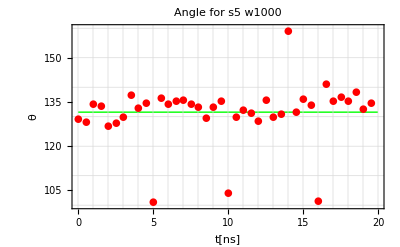

```mathematica
Show[Plot[{model/.fit51t},{x,0,20},PlotStyle->{Green,Thick}],ListPlot[t51t,PlotMarkers->{●,10},PlotStyle->Red],GridLines->{{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},{100,110,120,130,140,150,160}},PlotRange->{{0,20},{100,160}},Frame->True,FrameTicks->Automatic, AxesLabel->{"t[ns]","θ"},PlotLabel->"Angle for s5 w1000"]
```

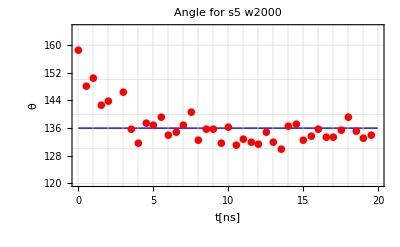

```mathematica
Show[Plot[{model/.fit52t},{x,0,20},PlotStyle->{Blue,Thick}],ListPlot[t52t,PlotMarkers->{●,10},PlotStyle->Red],PlotRange->{{0,20},{120,165}},GridLines->{{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},{100,110,120,130,140,150,160}},Frame->True,FrameTicks->Automatic, AxesLabel->{"t[ns]","θ"},PlotLabel->"Angle for s5 w2000"]
```

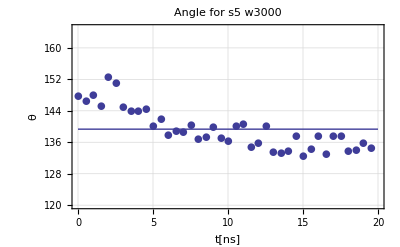

```mathematica
Show[Plot[{model/.fit53t},{x,0,20}],ListPlot[t53t,PlotMarkers->{●,10}],PlotRange->{{0,20},{120,165}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, AxesLabel->{"t[ns]","θ"},PlotLabel->"Angle for s5 w3000"]
```

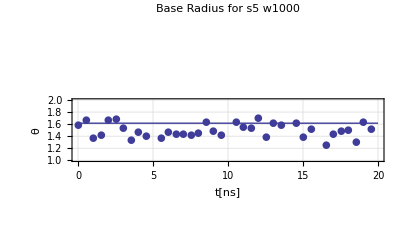

```mathematica
Show[Plot[{model/.fit51r},{x,0,20}],ListPlot[r51t,PlotMarkers->{●,10}],PlotRange->{{0,20},{1,2}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, AxesLabel->{"t[ns]","θ"},PlotLabel->"Base Radius for s5 w1000"]
```

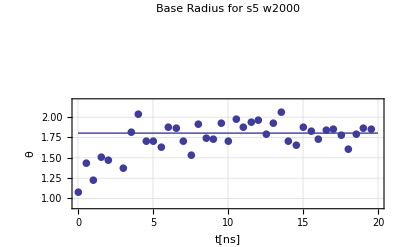

```mathematica
Show[Plot[{model/.fit52r},{x,0,20}],ListPlot[r52t,PlotMarkers->{●,10}],PlotRange->{{0,20},{0.9,2.2}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, AxesLabel->{"t[ns]","θ"},PlotLabel->"Base Radius for s5 w2000"]
```

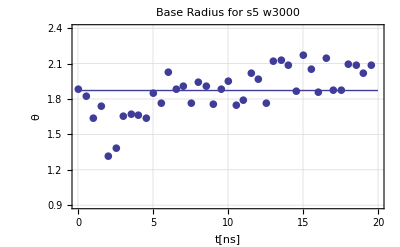

```mathematica
Show[Plot[{model/.fit53r},{x,0,20}],ListPlot[r53t,PlotMarkers->{●,10}],PlotRange->{{0,20},{0.9,2.4}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, AxesLabel->{"t[ns]","θ"},PlotLabel->"Base Radius for s5 w3000"]
```

```mathematica
Only last 5ns
```

```mathematica
t51Last=input[[{31,32,33,34,35,36,37,38,39,40},2]]
t52Last=input[[{72,73,74,75,76,77,78,79,80,81},2]];
t53Last=input[[{113,114,115,116,117,118,119,120,121,122},2]];

r51Last=input[[{31,32,33,34,35,36,37,38,39,40},3]]
r52Last=input[[{72,73,74,75,76,77,78,79,80,81},3]];
r53Last=input[[{113,114,115,116,117,118,119,120,121,122},3]];
```

{136.168,133.816,101.401,141.251,135.354,136.611,135.234,138.493,132.54,134.505}

{1.39136,1.51518,3.62905,1.25811,1.43937,1.48239,1.50546,1.30306,1.62828,1.51382}

```mathematica
tLast={15,15.5,16,16.5,17,17.5,18,18.5,19,19.5};
```

```mathematica
t51tLast=Thread[{tLast,t51Last}]
t52tLast=Thread[{tLast,t52Last}]
t53tLast=Thread[{tLast,t53Last}]
r51tLast=Thread[{tLast,r51Last}]
r52tLast=Thread[{tLast,r52Last}]
r53tLast=Thread[{tLast,r53Last}]
```

{{15,136.168},{15.5,133.816},{16,101.401},{16.5,141.251},{17,135.354},{17.5,136.611},{18,135.234},{18.5,138.493},{19,132.54},{19.5,134.505}}

{{15,132.522},{15.5,133.656},{16,135.748},{16.5,133.399},{17,133.34},{17.5,135.364},{18,139.086},{18.5,135.229},{19,133.259},{19.5,134.103}}

{{15,132.425},{15.5,134.257},{16,137.467},{16.5,132.908},{17,137.523},{17.5,137.483},{18,133.794},{18.5,134.14},{19,135.86},{19.5,134.51}}

{{15,1.39136},{15.5,1.51518},{16,3.62905},{16.5,1.25811},{17,1.43937},{17.5,1.48239},{18,1.50546},{18.5,1.30306},{19,1.62828},{19.5,1.51382}}

{{15,1.87993},{15.5,1.83451},{16,1.73506},{16.5,1.83859},{17,1.8524},{17.5,1.78674},{18,1.61138},{18.5,1.79492},{19,1.86636},{19.5,1.85165}}

{{15,2.17041},{15.5,2.05809},{16,1.85931},{16.5,2.14676},{17,1.87607},{17.5,1.87241},{18,2.09598},{18.5,2.08521},{19,2.01676},{19.5,2.09103}}

```mathematica
fit51tLast=FindFit[t51tLast,model,{a},x]
fit52tLast=FindFit[t52tLast,model,{a},x]
fit53tLast=FindFit[t53tLast,model,{a},x]
fit51rLast=FindFit[r51tLast,model,{a},x]
fit52rLast=FindFit[r52tLast,model,{a},x]
fit53rLast=FindFit[r53tLast,model,{a},x]
```

{a→132.537}

{a→134.571}

{a→135.036}

{a→1.66661}

{a→1.80516}

{a→2.0272}

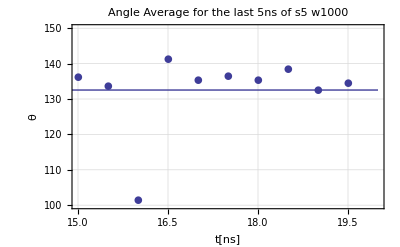

```mathematica
Show[Plot[{model/.fit51tLast},{x,0,20}],ListPlot[t51tLast,PlotMarkers->{●,10}],PlotRange->{{15,20},{100,150}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, AxesLabel->{"t[ns]","θ"},PlotLabel->"Angle Average for the last 5ns of s5 w1000"]
```

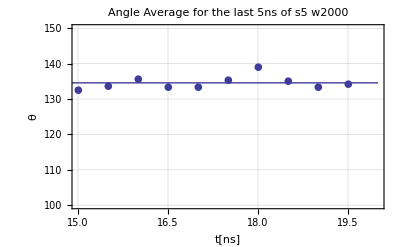

```mathematica
Show[Plot[{model/.fit52tLast},{x,0,20}],ListPlot[t52tLast,PlotMarkers->{●,10}],PlotRange->{{15,20},{100,150}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, AxesLabel->{"t[ns]","θ"},PlotLabel->"Angle Average for the last 5ns of s5 w2000"]
```

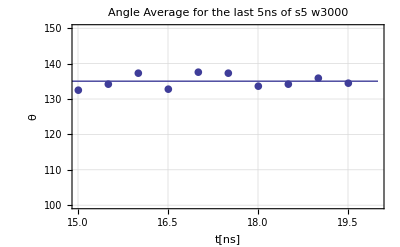

```mathematica
Show[Plot[{model/.fit53tLast},{x,0,20}],ListPlot[t53tLast,PlotMarkers->{●,10}],PlotRange->{{15,20},{100,150}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, AxesLabel->{"t[ns]","θ"},PlotLabel->"Angle Average for the last 5ns of s5 w3000"]
```

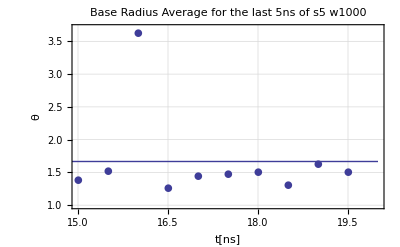

```mathematica
Show[Plot[{model/.fit51rLast},{x,0,20}],ListPlot[r51tLast,PlotMarkers->{●,10}],PlotRange->{{15,20},{1,3.7}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, AxesLabel->{"t[ns]","θ"},PlotLabel->"Base Radius Average for the last 5ns of s5 w1000"]
```

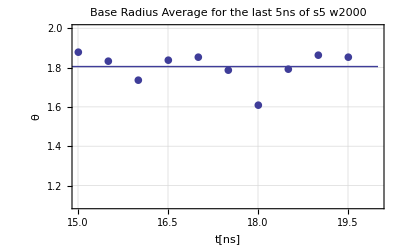

```mathematica
Show[Plot[{model/.fit52rLast},{x,0,20}],ListPlot[r52tLast,PlotMarkers->{●,10}],PlotRange->{{15,20},{1.1,2}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, AxesLabel->{"t[ns]","θ"},PlotLabel->"Base Radius Average for the last 5ns of s5 w2000"]
```

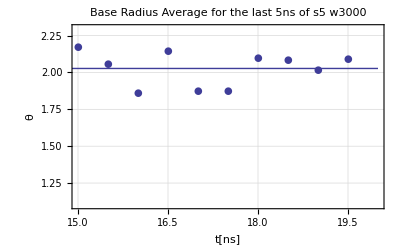

```mathematica
Show[Plot[{model/.fit53rLast},{x,0,20}],ListPlot[r53tLast,PlotMarkers->{●,10}],PlotRange->{{15,20},{1.1,2.3}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, AxesLabel->{"t[ns]","θ"},PlotLabel->"Base Radius Average for the last 5ns of s5 w3000"]
```